Sinc

```mathematica
$Assumptions={τ>0,τR>0,t>=0,τ-t>=0,u>=0,τ-u>=0};
```

```mathematica
(* Relaxation function *)
```

```mathematica
Psi[t_]= Sinc[π t/(2τR)];
dPsi[t_]=D[Psi[t],t];
ddPsi[t_]=D[dPsi[t],t];
```

```mathematica
(* Dirac delta coefficients *)
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=((-4+π^2) τR^2)/π^2;
```

```mathematica
(* Parameters and protocol *)
```

```mathematica
τR=1;

g[t_]=(t+τR)/(τ+2τR);
h1[t_]=t/τ;
dh1[t_]=h1'[t];
h2[t_]=(t/τ)^2;
dh2[t_]=h2'[t];
h3[t_]=(t/τ)^3;
dh3[t_]=h3'[t];
```

```mathematica
(* Calculation of the irreversible works *)
```

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]
```

1/2-(8 τ-π^2 τ (2+2 τ+τ^2)-8 τ Cos[(π τ)/2]+4 π (1+τ) Sin[(π τ)/2])/(2 π^2 τ (2+τ)^2)-(π+π τ-(2 Sin[(π τ)/2])/τ-2 SinIntegral[(π τ)/2])/(π (2+τ))

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 Limit[ddPsi[t],t->0]+c0^2/(τ+2τR)^2 ddPsi[τ]
```

1/2+((-4+π^2)^2)/(12 π^2 (2+τ)^2)+((-4+π^2) (-π τ^2+π τ Cos[(π τ)/2]+2 (-1+τ) Sin[(π τ)/2]))/(π^3 τ^2 (2+τ)^2)+((-4+π^2) ((2 Cos[(π τ)/2])/(π τ)-(4 Sin[(π τ)/2])/(π^2 τ^2)))/(2 π (2+τ))+((-4+π^2)^2 (-(4 Cos[(π τ)/2])/(π τ^2)+(8 Sin[(π τ)/2])/(π^2 τ^3)-Sin[(π τ)/2]/τ))/(2 π^3 (2+τ)^2)-(8 τ-π^2 τ (2+2 τ+τ^2)-8 τ Cos[(π τ)/2]+4 π (1+τ) Sin[(π τ)/2])/(2 π^2 τ (2+τ)^2)-((-4+π^2) (π τ^2+π τ (1+τ) Cos[(π τ)/2]-2 (1+2 τ) Sin[(π τ)/2]))/(π^3 τ^2 (2+τ)^2)-(π+π τ-(2 Sin[(π τ)/2])/τ-2 SinIntegral[(π τ)/2])/(π (2+τ))

```mathematica
Wh1[τ_]=1/2 Integrate[Psi[t-u]dh1[t]dh1[u],{t,0,τ},{u,0,τ}]
```

(2 (-2+2 Cos[(π τ)/2]+π τ SinIntegral[(π τ)/2]))/(π^2 τ^2)

```mathematica
Wh2[τ_]=1/2 Integrate[Psi[t-u]dh2[t]dh2[u],{t,0,τ},{u,0,τ}]
```

(8 (-8-3 π^2 τ^2+2 (4+π^2 τ^2) Cos[(π τ)/2]+4 π τ Sin[(π τ)/2]+π^3 τ^3 SinIntegral[(π τ)/2]))/(3 π^4 τ^4)

```mathematica
Wh3[τ_]=1/2 Integrate[Psi[t-u]dh3[t]dh3[u],{t,0,τ},{u,0,τ}]
```

(18 (-128-5 π^4 τ^4+2 (64-8 π^2 τ^2+π^4 τ^4) Cos[(π τ)/2]+4 π τ (16+π^2 τ^2) Sin[(π τ)/2]+π^5 τ^5 SinIntegral[(π τ)/2]))/(5 π^6 τ^6)

```mathematica
(* Irreversible works *)
```

```mathematica
W0[τ_]=1/2-(8 τ-π^2 τ (2+2 τ+τ^2)-8 τ Cos[(π τ)/2]+4 π (1+τ) Sin[(π τ)/2])/(2 π^2 τ (2+τ)^2)-(π+π τ-(2 Sin[(π τ)/2])/τ-2 SinIntegral[(π τ)/2])/(π (2+τ));

W1[τ_]=1/2+((-4+π^2)^2)/(12 π^2 (2+τ)^2)+((-4+π^2) (-π τ^2+π τ Cos[(π τ)/2]+2 (-1+τ) Sin[(π τ)/2]))/(π^3 τ^2 (2+τ)^2)+((-4+π^2) ((2 Cos[(π τ)/2])/(π τ)-(4 Sin[(π τ)/2])/(π^2 τ^2)))/(2 π (2+τ))+((-4+π^2)^2 (-(4 Cos[(π τ)/2])/(π τ^2)+(8 Sin[(π τ)/2])/(π^2 τ^3)-Sin[(π τ)/2]/τ))/(2 π^3 (2+τ)^2)-(8 τ-π^2 τ (2+2 τ+τ^2)-8 τ Cos[(π τ)/2]+4 π (1+τ) Sin[(π τ)/2])/(2 π^2 τ (2+τ)^2)-((-4+π^2) (π τ^2+π τ (1+τ) Cos[(π τ)/2]-2 (1+2 τ) Sin[(π τ)/2]))/(π^3 τ^2 (2+τ)^2)-(π+π τ-(2 Sin[(π τ)/2])/τ-2 SinIntegral[(π τ)/2])/(π (2+τ));
Wh1[τ_]=(2 (-2+2 Cos[(π τ)/2]+π τ SinIntegral[(π τ)/2]))/(π^2 τ^2);
Wh2[τ_]=(8 (-8-3 π^2 τ^2+2 (4+π^2 τ^2) Cos[(π τ)/2]+4 π τ Sin[(π τ)/2]+π^3 τ^3 SinIntegral[(π τ)/2]))/(3 π^4 τ^4);
Wh3[τ_]=(18 (-128-5 π^4 τ^4+2 (64-8 π^2 τ^2+π^4 τ^4) Cos[(π τ)/2]+4 π τ (16+π^2 τ^2) Sin[(π τ)/2]+π^5 τ^5 SinIntegral[(π τ)/2]))/(5 π^6 τ^6);
```

```mathematica
(* Plot *)
```

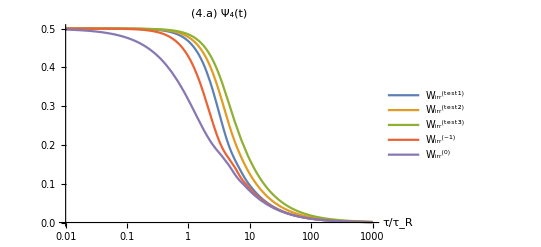

```mathematica
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test1)"],Legended[Wh2[τ],"W_irr^(test2)"],Legended[Wh3[τ],"W_irr^(test3)"],Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,1000},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}],PlotLabel->"(4.a) Ψ_4(t)"]
```

```mathematica
(* Error *)
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

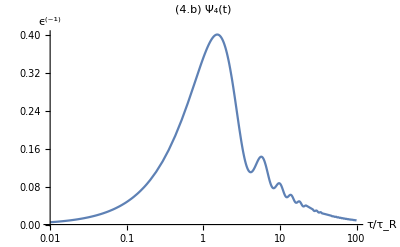

```mathematica
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^(-1)"},PlotLabel->"(4.b) Ψ_4(t)"]
```